```mathematica
Clear["Global`"];
server="localhost";
db=DatabaseReference[
<| "Backend" ->"PostgreSQL"
, "Name"->"bitcoin"
, "Port"-> Automatic
, "Host"->server
,"Username"->"rpc"
,"Password"->"YOURPASSWORD"|>
];
tip = ExternalEvaluate[db,"select * from blockstats where height in (select max(height) from blockstats);"]
```

```mathematica
txs = ExternalEvaluate[
db
,"select height, time, txs, subsidy, totalfee 
from blockstats 
order by height desc;"
]
```

Dataset[<>]

```mathematica
data={#"height",#"subsidy"+#"totalfee"}&/@txs;
```

```mathematica
ListPlot[data
,PlotRange->All
, ImageSize->Full
, GridLines->{
Range[0,10^6,210000]
,Join[Range[0,500,50],{25,12.5,6.25.3.125}]
}
]
```

-Graphics-

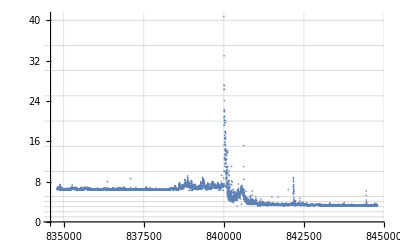

```mathematica
data10k=Take[data,10000];
ListPlot[data10k
,PlotRange->All
,ImageSize->Full
, GridLines->{Automatic,Join[Range[4],Range[0,50,5]]}
]
```

```mathematica
Take[ReverseSortBy[data,Last ],50]
```

```mathematica
empty = ExternalEvaluate[db,"select count(*) from blockstats where txs=1;"]
```

```mathematica
tip//Normal
```

{<|height→844796,blockhash→000000000000000000011e047b8d866d0299f2052af2ec9db9c6edc50734053e,avgfee→2473,avgfeerate→13,avgtxsize→278,ins→7096,outs→14142,subsidy→3.125,swtotal_size→1541511,swtotal_weight→3879411,swtxs→5518,time→1716493828,total_out→158432994690,total_size→1569603,total_weight→3991779,totalfee→0.139227,txs→5630,utxo_increase→7046,utxo_size_inc→468377,maxfee→820468,maxfeerate→504,maxtxsize→179986,medianfee→1388,mediantime→1716492214,mediantxsize→210,minfee→1069,minfeerate→5,mintxsize→150|>}

```mathematica
tip[[1]]["height"]/2016//N//Ceiling
```

420